### 十阶内的数据

```mathematica
chkQ[n_,subgraph_]:=Module[{graphs,selected,m},
graphs=gSet[n];
Print["time: ",Timing[
selected=Select[graphs,!IGSubisomorphicQ[subgraph,#]&];
m=(EdgeCount/@selected)//Max;
Print["Vertex number: ",n,"\nmaximal number of edges: ",m,"\ngraphs:"];
Print[Select[selected,EdgeCount@#==m&]];
""],"\n——————division line——————\n\n"]];
```

Vertex number: 5
maximal number of edges: 7
graphs:

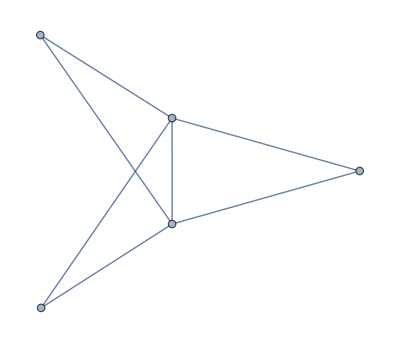
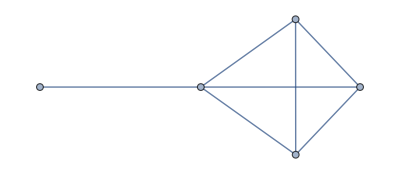
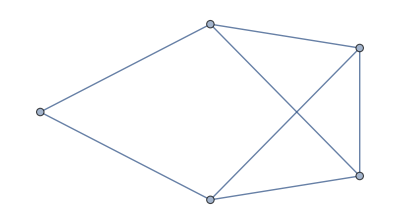

time: {0.036464,}
——————division line——————

Vertex number: 6
maximal number of edges: 10
graphs:

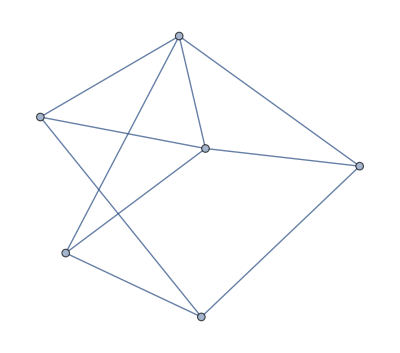

time: {0.017555,}
——————division line——————

Vertex number: 7
maximal number of edges: 13
graphs:

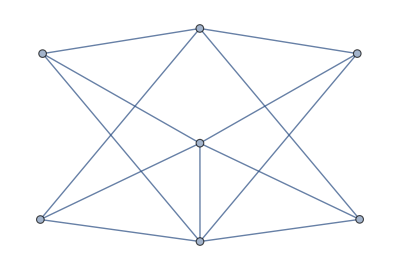
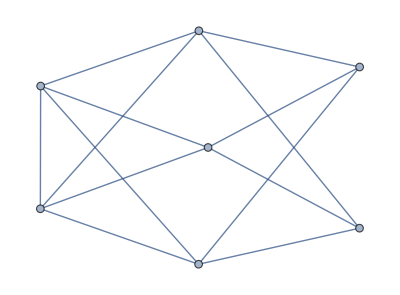

time: {0.10302,}
——————division line——————

Vertex number: 8
maximal number of edges: 17
graphs:

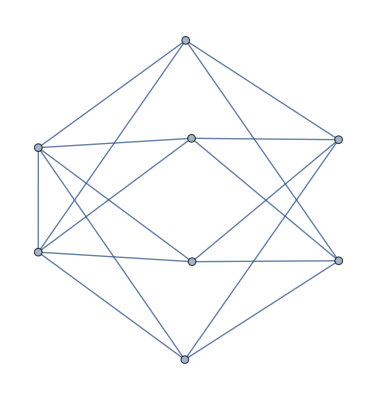

time: {0.747823,}
——————division line——————

Vertex number: 9
maximal number of edges: 21
graphs:

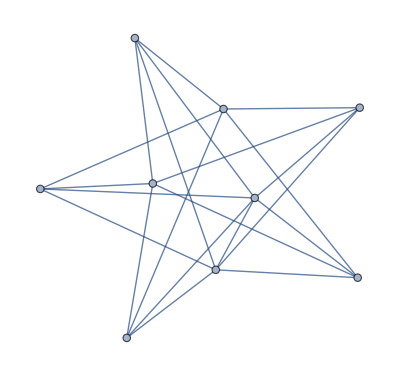
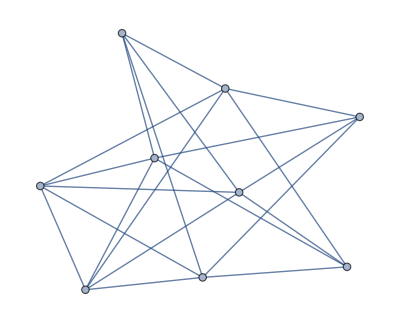

time: {17.2408,}
——————division line——————

```mathematica
chkQ[#,subgraph]&/@Range[5,10]
```

```mathematica
chkQ[10,subgraph]
```

$Aborted